```mathematica
Solve[Cos[x]==0, x]
```

{{x→ConditionalExpression[-π/2+2 π C[1],C[1]∈ℤ]},{x→ConditionalExpression[π/2+2 π C[1],C[1]∈ℤ]}}

```mathematica
xt = Pi/2
```

π/2

```mathematica
Cos[xt]Sin[xt]^2 omega^2 + g/l Sin[xt]
```

g/l

```mathematica
Cos[-xt]Sin[-xt]^2 omega^2 + g/l Sin[-xt]
```

-g/l

```mathematica
Cos[0]Sin[0]^2 omega^2 + g/l Sin[0]
```

0

```mathematica
D[1/Sin[x]^2, x]
```

-2 Cot[x] Csc[x]^2

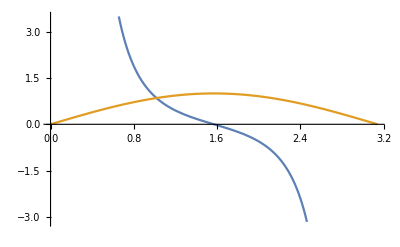

```mathematica
Plot[{Cos[x]/Sin[x]^3,Sin[x]},{x, 0, Pi}]
```

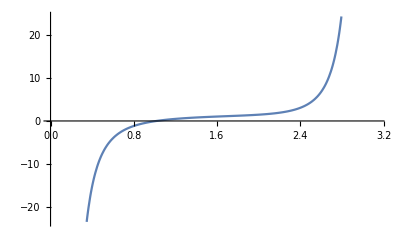

```mathematica
Plot[{Sin[x]-Cos[x]/Sin[x]^3},{x, 0, Pi}]
```

```mathematica
3.14*3/4
```

2.355

```mathematica
D[Cos[x]/Sin[x]^3, x]
```

-2 Cot[x]^2 Csc[x]^2-Csc[x]^4

```mathematica
Simplify[%]
```

-(2+Cos[2 x]) Csc[x]^4

```mathematica
J= m l^2 Sin[θ]^2 dϕ
```

dϕ l^2 m Sin[θ]^2

```mathematica
Cos[θ]Sin[θ]dϕ^2 - g/l Sin[θ]==-(J^2/(2 m^2 l^4)Cos[θ]/Sin[θ]^3- g/l Sin[θ])
```

-(g Sin[θ])/l+dϕ^2 Cos[θ] Sin[θ]==(g Sin[θ])/l-1/2 dϕ^2 Cos[θ] Sin[θ]

```mathematica
-(g/l Sin[θ]-J^2/(2 m^2 l^4)Cos[θ]/Sin[θ]^3)
```

-(g Sin[θ])/l+1/2 dϕ^2 Cos[θ] Sin[θ]